```mathematica
x=Table[k,{k,100}]/100.
```

{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.}

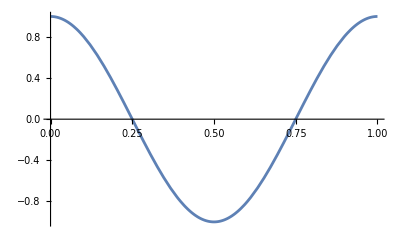
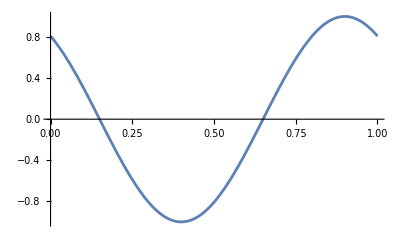
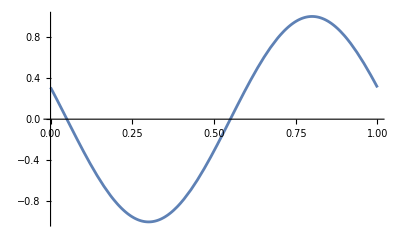
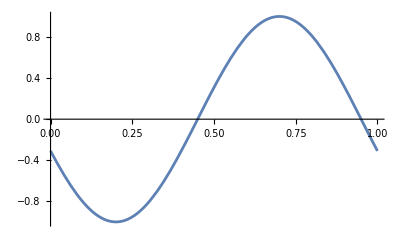
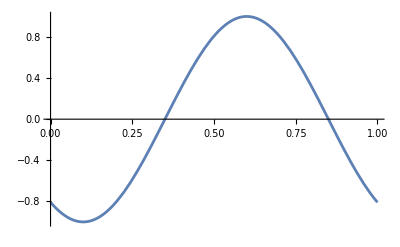
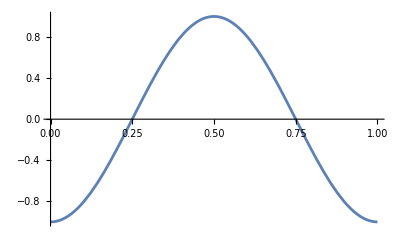
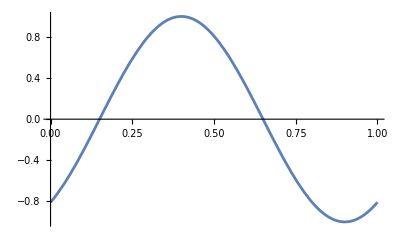
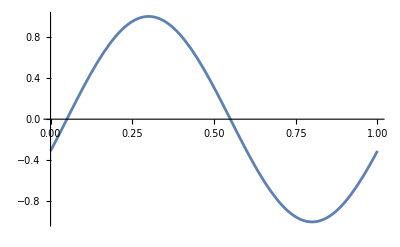

```mathematica
Table[Plot[Cos[2*Pi*(x+0.1*(i-1))],{x,0,1}],{i,10}]
```

```mathematica
g[x_]:=If[-Pi/2.<=x<=Pi/2.,Cos[x],0]
```

```mathematica
g1[x_]:=g[x*2*Pi]
```

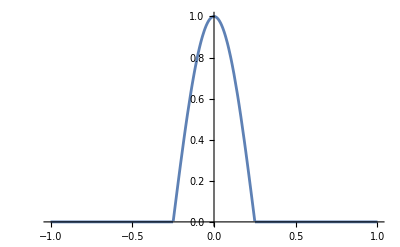

```mathematica
Plot[g1[x],{x,-1,1}]
```

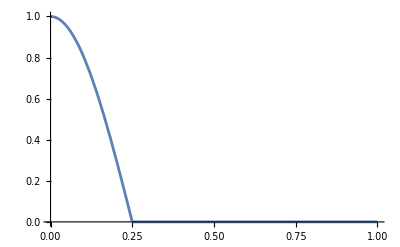
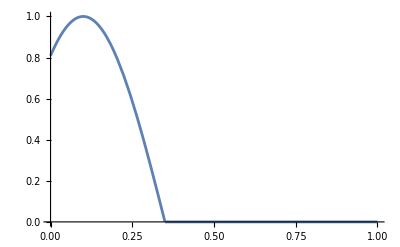
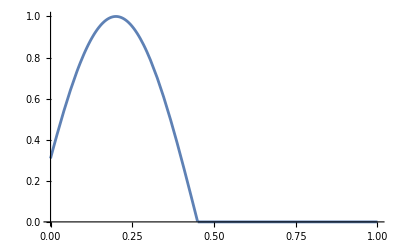
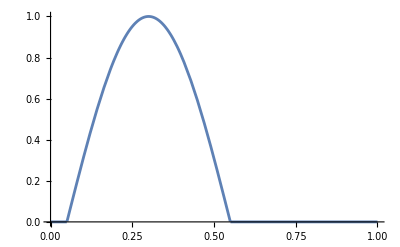
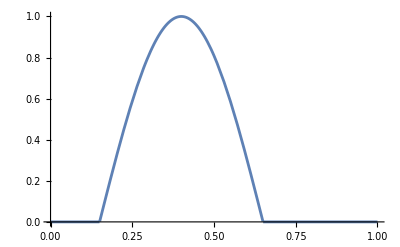
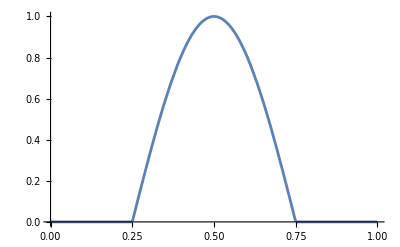
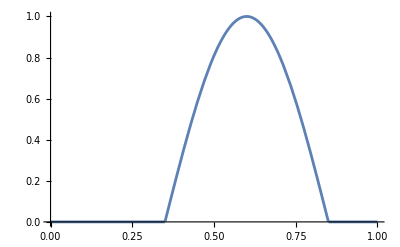
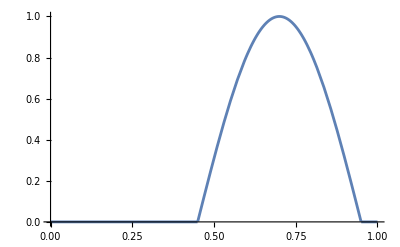

```mathematica
Table[Plot[g1[x-0.1*(i-1)],{x,0,1}],{i,10}]
```

```mathematica
y=Table[Table[g1[x-0.1*(i-1)],{x,0.1,1,0.1}],{i,10}]
```

{{0.809017,0.309017,0,0,0,0,0,0,0,0},{1.,0.809017,0.309017,0,0,0,0,0,0,0},{0.809017,1.,0.809017,0.309017,0,0,0,0,0,0},{0.309017,0.809017,1.,0.809017,0.309017,0,0,0,0,0},{0,0.309017,0.809017,1.,0.809017,0.309017,0,0,0,0},{0,0,0.309017,0.809017,1.,0.809017,0.309017,0,0,0},{0,0,0,0.309017,0.809017,1.,0.809017,0.309017,0,0},{0,0,0,0,0.309017,0.809017,1.,0.809017,0.309017,0},{0,0,0,0,0,0.309017,0.809017,1.,0.809017,0.309017},{0,0,0,0,0,0,0.309017,0.809017,1.,0.809017}}

```mathematica
Dimensions[y]
```

{10,10}

```mathematica
MatrixForm[y]
```

(0.809017 | 0.309017 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1. | 0.809017 | 0.309017 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.809017 | 1. | 0.809017 | 0.309017 | 0 | 0 | 0 | 0 | 0 | 0
0.309017 | 0.809017 | 1. | 0.809017 | 0.309017 | 0 | 0 | 0 | 0 | 0
0 | 0.309017 | 0.809017 | 1. | 0.809017 | 0.309017 | 0 | 0 | 0 | 0
0 | 0 | 0.309017 | 0.809017 | 1. | 0.809017 | 0.309017 | 0 | 0 | 0
0 | 0 | 0 | 0.309017 | 0.809017 | 1. | 0.809017 | 0.309017 | 0 | 0
0 | 0 | 0 | 0 | 0.309017 | 0.809017 | 1. | 0.809017 | 0.309017 | 0
0 | 0 | 0 | 0 | 0 | 0.309017 | 0.809017 | 1. | 0.809017 | 0.309017
0 | 0 | 0 | 0 | 0 | 0 | 0.309017 | 0.809017 | 1. | 0.809017)

```mathematica
yt=Transpose[y];
```

```mathematica
MatrixForm[yt]
```

(0.809017 | 1. | 0.809017 | 0.309017 | 0 | 0 | 0 | 0 | 0 | 0
0.309017 | 0.809017 | 1. | 0.809017 | 0.309017 | 0 | 0 | 0 | 0 | 0
0 | 0.309017 | 0.809017 | 1. | 0.809017 | 0.309017 | 0 | 0 | 0 | 0
0 | 0 | 0.309017 | 0.809017 | 1. | 0.809017 | 0.309017 | 0 | 0 | 0
0 | 0 | 0 | 0.309017 | 0.809017 | 1. | 0.809017 | 0.309017 | 0 | 0
0 | 0 | 0 | 0 | 0.309017 | 0.809017 | 1. | 0.809017 | 0.309017 | 0
0 | 0 | 0 | 0 | 0 | 0.309017 | 0.809017 | 1. | 0.809017 | 0.309017
0 | 0 | 0 | 0 | 0 | 0 | 0.309017 | 0.809017 | 1. | 0.809017
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.309017 | 0.809017 | 1.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.309017 | 0.809017)

```mathematica
Export["~/cross_corr_chatgpt/input.csv",yt,"CSV"]
```

~/cross_corr_chatgpt/input.csv

```mathematica
a=Import["~/cross_corr_chatgpt/input.csv","CSV"]
```

{{0.809017,1.,0.809017,0.309017,0,0,0,0,0,0},{0.309017,0.809017,1.,0.809017,0.309017,0,0,0,0,0},{0,0.309017,0.809017,1.,0.809017,0.309017,0,0,0,0},{0,0,0.309017,0.809017,1.,0.809017,0.309017,0,0,0},{0,0,0,0.309017,0.809017,1.,0.809017,0.309017,0,0},{0,0,0,0,0.309017,0.809017,1.,0.809017,0.309017,0},{0,0,0,0,0,0.309017,0.809017,1.,0.809017,0.309017},{0,0,0,0,0,0,0.309017,0.809017,1.,0.809017},{0,0,0,0,0,0,0,0.309017,0.809017,1.},{0,0,0,0,0,0,0,0,0.309017,0.809017}}

```mathematica
at=Transpose[a]
```

{{0.809017,0.309017,0,0,0,0,0,0,0,0},{1.,0.809017,0.309017,0,0,0,0,0,0,0},{0.809017,1.,0.809017,0.309017,0,0,0,0,0,0},{0.309017,0.809017,1.,0.809017,0.309017,0,0,0,0,0},{0,0.309017,0.809017,1.,0.809017,0.309017,0,0,0,0},{0,0,0.309017,0.809017,1.,0.809017,0.309017,0,0,0},{0,0,0,0.309017,0.809017,1.,0.809017,0.309017,0,0},{0,0,0,0,0.309017,0.809017,1.,0.809017,0.309017,0},{0,0,0,0,0,0.309017,0.809017,1.,0.809017,0.309017},{0,0,0,0,0,0,0.309017,0.809017,1.,0.809017}}

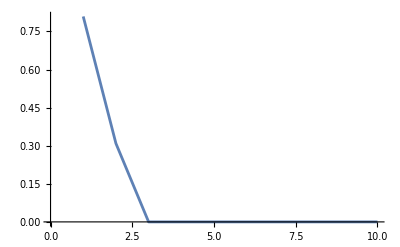
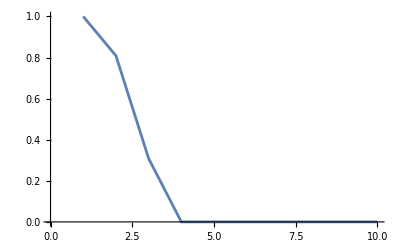
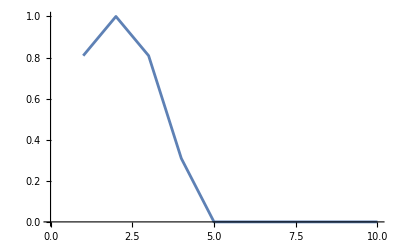
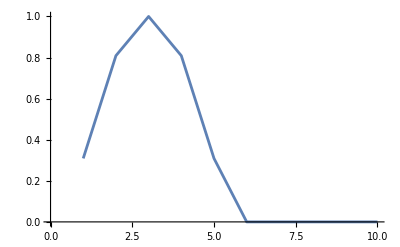
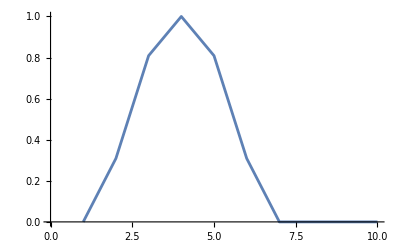
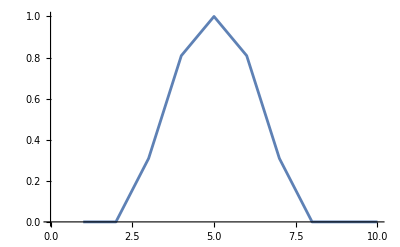
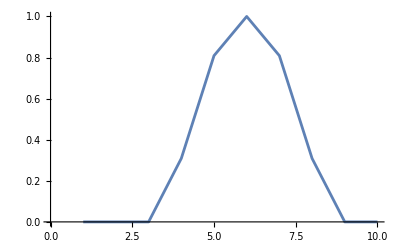
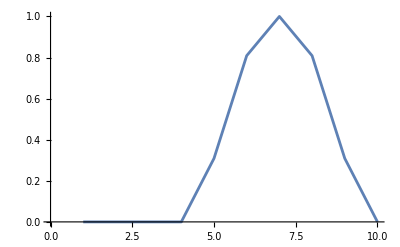

```mathematica
Table[ListPlot[at[[i]],Joined->True],{i,Length[at]}]
```